## Correlator ,⟨TTTT⟩

### Conformal blocks in position space

```mathematica
g[h_][z_]=z^h Hypergeometric2F1[h,h,2h,z];
```

### Conformal blocks in momentum space

```mathematica
SetDirectory[NotebookDirectory[]];
<<MSCB2d`
```

MSCB2d is a Mathematica package that evaluates
Momentum-Space Conformal Blocks in a 2d CFT.

The Wightman 4-point function
  ⟨Ω|O_4(p_4)O_3(p_3)O_2(p_2)O_1(p_1)|Ω⟩
    = (2π)^2 δ(p_1+p_2+p_3+p_4) G(p_a)
admits the conformal block expansion
  G(p_a)=∑_x  λ_(12  x)λ_x34 G_x(p_a)
This package provides explicit expressions for G_x
as a function of the conformal weights (h_a,(h̄)_a) of
the external (1,2,3,4) and exchange (x) operators
and of the momenta p_a.

The following conventions are used for the momenta:
  p_i=p_1   
  p_f=-p_4
  k=p_1+p_2=-p_3-p_4
The 4-point function is identically zero unless
all 3 momenta p_i, p_f and k lie in the future
light-cone.

### Correlation function in position space

```mathematica
Gdisc[z_]=c^2/4(1+z^4+(z/(1-z))^4);
Gconn[z_]=2c(z^2(1-z+z^2))/(1-z)^2;
G[z_]=Gconn[z]+Gdisc[z];
```

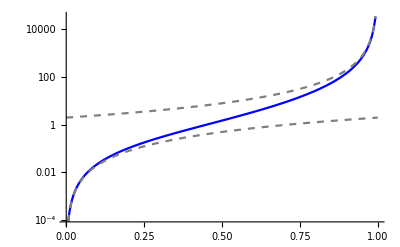

```mathematica
LogPlot[{Gconn[z]/c,2 z^2,2/(1-z)^2},{z,0,1},PlotStyle->{{Blue},{Gray,Dashed},{Gray,Dashed}}]
```

```mathematica
Simplify[1/((z1-z2)^4(z3-z4)^4)Gdisc[((z1-z2)(z3-z4))/((z1-z3)(z2-z4))]==c^2/4(1/((z1-z2)^4(z3-z4)^4)+1/((z1-z3)^4(z2-z4)^4)+1/((z1-z4)^4(z2-z3)^4)),z1>z2>z3>z4]
```

True

```mathematica
Simplify[1/((z1-z2)^4(z3-z4)^4)Gconn[((z1-z2)(z3-z4))/((z1-z3)(z2-z4))]==c(1/((z1-z2)^2(z1-z3)^2(z2-z4)^2(z3-z4)^2)+1/((z1-z2)^2(z1-z4)^2(z2-z3)^2(z3-z4)^2)+1/((z1-z3)^2(z1-z4)^2(z2-z3)^2(z2-z4)^2)),z1>z2>z3>z4]
```

True

### OPE limit

In the limit of coincident points, the OPE T×T satisfies
	T(z_1)T(z_2)=(c/2)/(z_1-z_2)^4+(2T(z_1))/(z_1-z_2)^2+...
see eq. (5.121) in the Big Yellow Book.

This implies that in the double limit z_2→z_1, z_3→z_4, we have
	⟨T(z_1)T(z_2)T(z_3)T(z_4)⟩
	=(c^2/4)/((z_1-z_2)^4(z_4-z_3)^4)+4/((z_1-z_2)^2(z_4-z_3)^2)⟨T(z_1)T(z_4)⟩
	=(c^2/4)/((z_1-z_2)^4(z_4-z_3)^4)+(2c)/((z_1-z_2)^2(z_4-z_3)^2(z_1-z_4)^4)+...

```mathematica
Series[1/((z1-z2)^4(z3-z4)^4)G[((z1-z2)(z3-z4))/((z1-z3)(z2-z4))],{z2,z1,-2},{z3,z4,-2}]//Normal
```

c^2/(4 (-z1+z2)^4 (z3-z4)^4)+(2 c)/((-z1+z2)^2 (z1-z4)^4 (z3-z4)^2)

### Conformal block expansion in position space

One can split the OPE coefficients into a piece contributing to the connected part and a piece contributing to the disconnected part, with different scalings in c:

```mathematica
λdisc[h_]=c^2/4((h-3)(h-2)(h-1)!(h+2)!)/(36(2h-3)!)
```

(c^2 (-3+h) (-2+h) (-1+h)! (2+h)!)/(144 (-3+2 h)!)

```mathematica
Series[4/c^2 Gdisc[z],{z,0,20}]
%==Series[4/c^2(c^2/4 g[0][z]+Sum[λdisc[h]g[h][z],{h,2,20,2}]),{z,0,20}]
```

1+2 z^4+4 z^5+10 z^6+20 z^7+35 z^8+56 z^9+84 z^10+120 z^11+165 z^12+220 z^13+286 z^14+364 z^15+455 z^16+560 z^17+680 z^18+816 z^19+969 z^20+O[z]^21

True

```mathematica
λconn[h_]=2c((h^2-h-1)(h-1)!(h-2)!)/((2h-3)!)
```

(2 c (-1-h+h^2) (-2+h)! (-1+h)!)/((-3+2 h)!)

```mathematica
Series[1/(2c) Gconn[z],{z,0,20}]
%==Series[1/(2c)(Sum[λconn[h]g[h][z],{h,2,20,2}]),{z,0,20}]
```

z^2+z^3+2 z^4+3 z^5+4 z^6+5 z^7+6 z^8+7 z^9+8 z^10+9 z^11+10 z^12+11 z^13+12 z^14+13 z^15+14 z^16+15 z^17+16 z^18+17 z^19+18 z^20+O[z]^21

True

```mathematica
λ[h_]=λdisc[h]+λconn[h];
```

```mathematica
Table[λ[h]==2c((h-1)!(h-2)!)/((2h-3)!)(h^2-h-1+c((h-3)(h-2)(h-1)h(h+1)(h+2))/288)//Simplify,{h,2,20,2}]//DeleteDuplicates
```

{True}

The OPE coefficients of the disconnected part do not decay as fast as those of the connected part at large h:

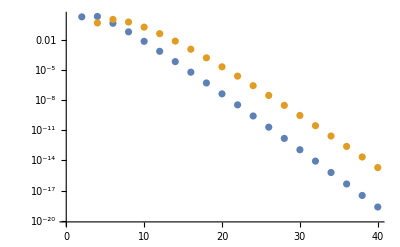

```mathematica
ListLogPlot[{Table[{h,λconn[h]/c},{h,2,40,2}],Table[{h,λdisc[h]/c^2},{h,2,40,2}]}]
```

### Correlation function in momentum space

This is the result of a direct Fourier transform for the connected part (at c=2 for definiteness):

```mathematica
Wconn[pf_,k_,pi_]:=If[pi≤0||pf≤0,0,If[pi>pf,Wconn[pi,k,pf],
1/(3 √2)(2π)^3 Piecewise[{
{k^3(2 pi-k)(2pf-k),k>0&&k<pi},
{pi^3(2pf-k)(2k-pi),k≥pi&&k<pf},
{pi^3(2pf-pi)(2k-pi-pf)-(pf-pi+k)(pf-pi-k)(pf+pi-k)^3,k≥pf&&k<pi+pf},
{pi^3(2pf-pi)(2k-pi-pf),k≥pi+pf}
},
0
]
]]
```

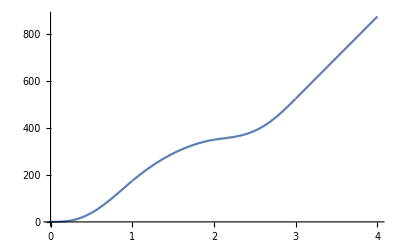

```mathematica
Plot[Wconn[2,k,1],{k,0,4}]
```

First and second derivatives:

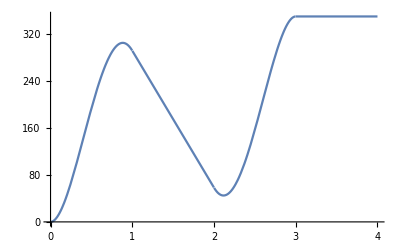

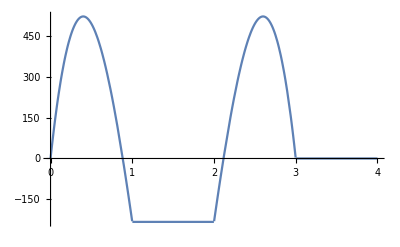

```mathematica
D[Wconn[2,k,1],k];
Plot[%,{k,0,4}]
D[Wconn[2,k,1],{k,2}];
Plot[%,{k,0,4}]
```

Limit p_i→0

```mathematica
Wconn0[p_,k_]:=1/3(2π)^4 If[p≤0||k≤0,0,
Piecewise[{
{k(2p-k),k<p},
{p(2k-p),k≥p}
}]
]
```

Other formulation:

```mathematica
Wconn1234[p3_,p2_,p1_]:=Module[{p,p4},
p=p1+p2;
p4=-p1-p2-p3;
If[p1≤0||p4≥0,0,If[p2+p3<0,Wconn1234[-p2,-p3,-p4],
1/(3 √2)(2π)^3 Piecewise[{
{p^3(p1-p2)(p3-p4),0<p<p1},
{p1^3(p3-p4)(p2-p3-p4),p1<p<-p4},
{p1^3(p2-p3)(p2+p3-p4)-(p1-p3)(p2-p4)(p2+p4)^3,-p4<p<p1-p4},
{p1^3(p2-p3)(p2+p3-p4),p1-p4<p}
},
0
]
]
]
]
```

```mathematica
Table[Module[{pf,k,pi,p4,p3,p2,p1},
pf=RandomReal[{0,1}];
k=RandomReal[{0,1}];
pi=RandomReal[{0,1}];
{p4,p3,p2,p1}={-pf,pf-k,k-pi,pi};
Wconn[pf,k,pi]/Wconn1234[p3,p2,p1]],{20}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

### Conformal block expansion in momentum space: disconnected part

```mathematica
Wdiscsum[n_][pf_,k_,pi_]:=Sum[λdisc[h]HolomorphicCB[2,h][-pf,k,pi],{h,2,n,2}]/.{c->2}
```

```mathematica
Plot3D[(Wdiscsum[10][pf,1,pi])/(2π)^4,{pi,0,1.2},{pf,0,1.2},PlotRange->All,Boxed->False,ColorFunction->"TemperatureMap",AxesLabel->{"p_i/k","p_f/k",""},BaseStyle->{14,FontFamily->"Latin Modern Roman"},PlotLabel->"4 operators",PlotPoints->100]
```

-Graphics3D-

```mathematica
Plot3D[(Wdiscsum[18][pf,1,pi])/(2π)^4,{pi,0,1.2},{pf,0,1.2},PlotRange->All,Boxed->False,ColorFunction->"TemperatureMap",AxesLabel->{"p_i/k","p_f/k",""},BaseStyle->{14,FontFamily->"Latin Modern Roman"},PlotLabel->"8 operators",PlotPoints->100]
```

-Graphics3D-

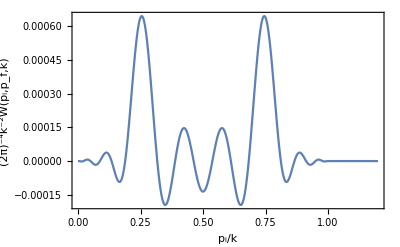

```mathematica
Plot[(Wdiscsum[22][1/4,1,pi])/(2π)^4,{pi,0,1.2},PlotRange->{{0,1.2},All},Axes->False,Frame->True,FrameLabel->{"p_i/k","(2π)^-4k^-2W(p_i,p_f,k)","k = 4 p_f      10 operators"},BaseStyle->{14,FontFamily->"Latin Modern Roman"}]
```

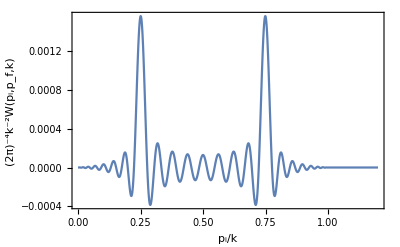

```mathematica
Plot[(Wdiscsum[52][1/4,1,pi])/(2π)^4,{pi,0,1.2},PlotRange->{{0,1.2},All},Axes->False,Frame->True,FrameLabel->{"p_i/k","(2π)^-4k^-2W(p_i,p_f,k)","k = 4 p_f      25 operators"},BaseStyle->{14,FontFamily->"Latin Modern Roman"}]
```

### Conformal block expansion in momentum space: connected part

```mathematica
HolomorphicCB[2,2][pf,k,pi]//Simplify
```

(48 √2 π^3 (Piecewise[{{-1/12 pf^3 (2 k+pf), k>0&&pf<0&&k+pf>0}, {-1/12 k^3 (k+2 pf), k>0&&pf<0&&k+pf<0}, {0, True}}]) (Piecewise[{{-1/12 k^3 (k-2 pi), pi>0&&k>0&&k<pi}, {1/12 (2 k-pi) pi^3, pi>0&&k>0&&k>pi}, {0, True}}]))/k^3

```mathematica
HolomorphicCB[2,4][pf,k,pi]//Simplify
HolomorphicCB[2,6][pf,k,pi]//Simplify
HolomorphicCB[2,8][pf,k,pi]//Simplify
```

Piecewise[{{0, pf≥0||k≤0||k+pf≤0||k≤pi||pi≤0}, {-(280 √2 pf^3 (k+pf)^3 (k-pi)^3 pi^3 π^3)/(9 k^7), True}}]

Piecewise[{{0, pf≥0||k≤0||k+pf≤0||k≤pi||pi≤0}, {-(154 √2 pf^3 (k+pf)^3 (2 k^2+9 k pf+9 pf^2) (k-pi)^3 pi^3 (2 k^2-9 k pi+9 pi^2) π^3)/k^11, True}}]

Piecewise[{{0, pf≥0||k≤0||k+pf≤0||k≤pi||pi≤0}, {-(2288 √2 pf^3 (k+pf)^3 (5 k^4+55 k^3 pf+198 k^2 pf^2+286 k pf^3+143 pf^4) (k-pi)^3 pi^3 (5 k^4-55 k^3 pi+198 k^2 pi^2-286 k pi^3+143 pi^4) π^3)/(5 k^15), True}}]

```mathematica
Simplify[HolomorphicCB[2,h][pf,k,pi],0<pi<-pf<k]
1/k Limit[k %,k->∞]
λconn[h]%==-(√2(2π)^3)/9 (pi^3 pf^3)/k c (2 h-1) (h^2-h-1)  //FullSimplify
```

-(2 √2 pf^3 pi^3 π^3 Gamma[2 h] Hypergeometric2F1[1-h,h,4,-pf/k] Hypergeometric2F1[1-h,h,4,pi/k])/(9 k Gamma[h]^2)

-(2 √2 pf^3 pi^3 π^3 Gamma[2 h])/(9 k Gamma[h]^2)

True

```mathematica
Wconnsum[n_][pf_,k_,pi_]:=Sum[λconn[h]HolomorphicCB[2,h][-pf,k,pi],{h,2,n,2}]/.{c->2}
```

```mathematica
plot[pi_,pf_,kmax_]:=Plot[{(Wconnsum[2][pf,k,pi])/((2π)^3 pi^5),(Wconnsum[4][pf,k,pi])/((2π)^3 pi^5),(Wconnsum[6][pf,k,pi])/((2π)^3 pi^5),(Wconnsum[8][pf,k,pi])/((2π)^3 pi^5),(Wconnsum[10][pf,k,pi])/((2π)^3 pi^5),Wconn[pf,k,pi]/((2π)^3 pi^5)},{k,0,kmax},PlotStyle->Join[Table[RGBColor[(5-n)/6,(5-n)/6,1],{n,5}],{{Thick,Dashed,Red}}],Frame->True,PlotRange->{{0,kmax},All},FrameLabel->{"k","⟨TTTT⟩/(2π)^3c(k_1)^5"},FrameTicks->{Automatic,{{{0,"0"},{pi,"k_1"},{pf,"-k_4"}},None}},BaseStyle->{14,FontFamily->"Latin Modern Roman"}]
```

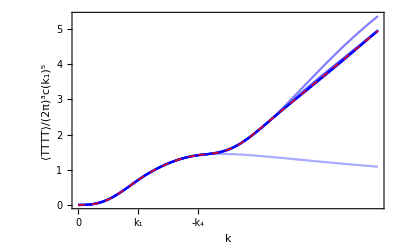

```mathematica
plot1=plot[1,2,5]
```

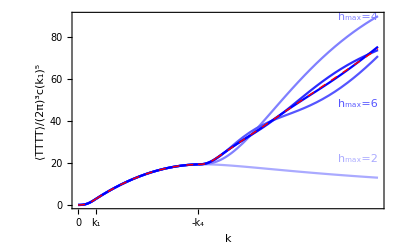

```mathematica
plot2=Show[plot[0.3,2.,5],Graphics[{
RGBColor[4/6,4/6,1],
Text["h_max=2",{5,22},{1.2,0}],
RGBColor[3/6,3/6,1],
Text["h_max=4",{5,90},{2,0}],
RGBColor[2/6,2/6,1],
Text["h_max=6",{5,48},{1.2,0}]}
]]
```

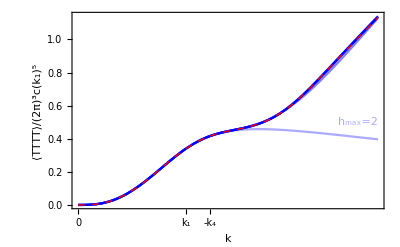

```mathematica
plot3=Show[plot[1.8,2.2,5],Graphics[{
RGBColor[4/6,4/6,1],
Text["h_max=2",{5,0.5},{1.2,0}]}
]]
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["TTTT_1.pdf",plot2]
Export["TTTT_2.pdf",plot3]*)
```

```mathematica
plotratio[pf_,k_,pimax_]:=Plot[{(Wconnsum[2][pf,k,pi])/Wconn[pf,k,pi],(Wconnsum[4][pf,k,pi])/Wconn[pf,k,pi],(Wconnsum[6][pf,k,pi])/Wconn[pf,k,pi],(Wconnsum[8][pf,k,pi])/Wconn[pf,k,pi],(Wconnsum[20][pf,k,pi])/Wconn[pf,k,pi]},{pi,0,pimax},PlotRange->{0,1.5},PlotStyle->{{Blue,Opacity[0.2]},{Blue,Opacity[0.4]},{Blue,Opacity[0.6]},{Blue,Opacity[0.8]},{Thick,Black}}]
```

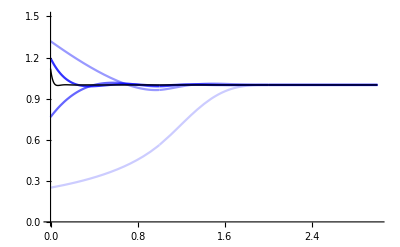

```mathematica
plotratio[1,2,3]
```

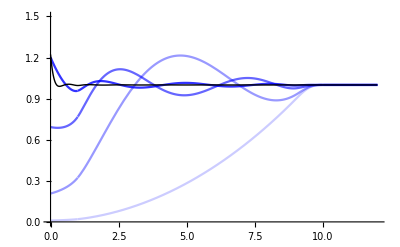

```mathematica
plotratio[1,10,12]
```

Note that the OPE cannot converge with a finite number of operators in the regime k>p_f, because each block is analytic over this regime while the 4-point function is not differentiable at k=p_i+p_f

Convergence in the worst case scenario: p_i^+<<p_f^+<<k^+

(2 √2 pf^3 pi^3 π^3 Gamma[2 h] Hypergeometric2F1[1-h,h,4,pf/k] Hypergeometric2F1[1-h,h,4,pi/k])/(9 k Gamma[h]^2)

(π^3 Gamma[2 h] Hypergeometric2F1[1-h,h,4,1/20])/(45 √2 Gamma[h]^2)

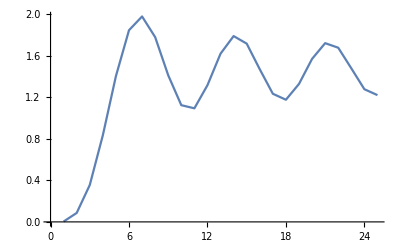

```mathematica
Simplify[HolomorphicCB[2,h][-pf,k,pi],0<pi<pf<k]
Limit[%/pi^3,pi->0]/.{pf->1,k->20}
Table[(λconn[h]%)/((2π)^4 c),{h,2,50,2}]//Accumulate//ListLinePlot
```